```mathematica
(*P1*)
x=3
```

3

```mathematica
y=2
```

2

```mathematica
x+y
```

5

```mathematica
x^2+y^2
```

13

```mathematica
x*y
```

6

```mathematica
x/y
```

3/2

```mathematica
(*P2*)
```

```mathematica
xs1=Sqrt[5]
```

√5

```mathematica
xs2=Sqrt[5.]
```

2.23607

```mathematica
xe1 =Exp[3.]
```

20.0855

```mathematica
xs3=Sin[Pi/3]
```

(√3)/2

```mathematica
xa1=ArcTan[Sqrt[3]]
```

π/3

```mathematica
xs1+xs2+xe1+xs3+xa1
```

26.4709

```mathematica
(*P3*)
```

```mathematica
f[x_]:=x^2+0.8
```

```mathematica
f[3]
```

9.8

```mathematica
f[Pi]
```

10.6696

```mathematica
f[1+t]
```

0.8+(1+t)^2

```mathematica
f[Sin[t*Pi]]
```

0.8+Sin[π t]^2

```mathematica
f[f[4.5]]
```

443.903

```mathematica
(*P4*)
f[a_]:=Sin[a^2]+Cos[a]
```

```mathematica
f[1]
```

Cos[1]+Sin[1]

```mathematica
f[1.]
```

1.38177

```mathematica
f[1.*Pi]
```

-1.4303

```mathematica
(*P5*)
f5[u_,v_]:=u/v
```

```mathematica
f5[21.,5.]
```

4.2

```mathematica
(*P6*)
f6[a_]:=a^2
```

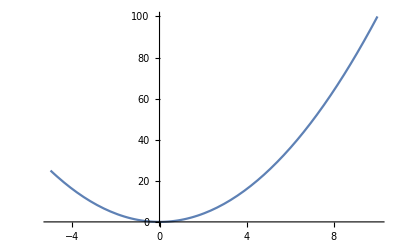

```mathematica
Plot[f6[a],{a,-5,10}]
```

```mathematica
f81[x_]:=Sin[x^2]
```

```mathematica
f82[x_]:=Cos[x^2]
```

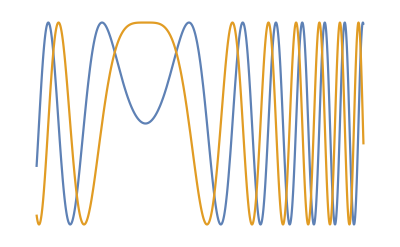

```mathematica
Plot[{f81[x],f82[x]},{x,-Pi,2Pi},Axes->False]
```

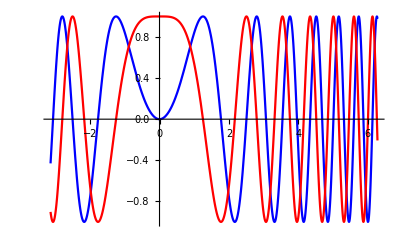

```mathematica
Plot[{f81[x],f82[x]},{x,-Pi,2Pi},PlotStyle->{Blue,Red},BaseStyle->{FontSize->14},Axes->True]
```

```mathematica
(*P7*)
f71[x_]:=Sin[x]
```

```mathematica
f72[x_]:=Cos[x]
```

```mathematica
f73[x_]:=1/(x+1)
```

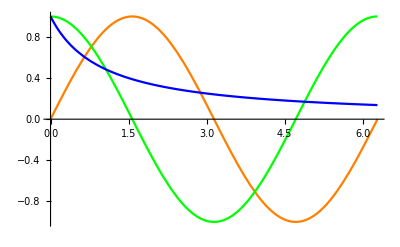

```mathematica
Plot[{f71[x],f72[x],f73[x]},{x,0,2Pi},PlotStyle->{Orange,Green,Blue},Axes->True]
```

```mathematica
(*P8*)
x10[t_]:=Cos[7t]Cos[11t]
```

```mathematica
y10[t_]:=Cos[7t]Sin[11t]
```

```mathematica
p10[t_]:={x10[t],y10[t]}
```

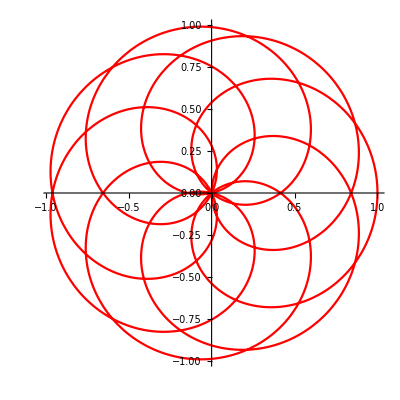

```mathematica
ParametricPlot[p10[t],{t,0,Pi},PlotStyle->Red,AspectRatio->1]
```

```mathematica
(*P9*)
x111[t_]:=Sin[t]
```

```mathematica
y111[t_]:=Cos[t^4]
```

```mathematica
x112[t_]:=Sin[t^2]
```

```mathematica
y112[t_]:=Cos[11*t]+Sqrt[t]
```

```mathematica
p111[t_]:={x111[t],y111[t]}
```

```mathematica
p112[t_]:={x112[t],y112[t]}
```

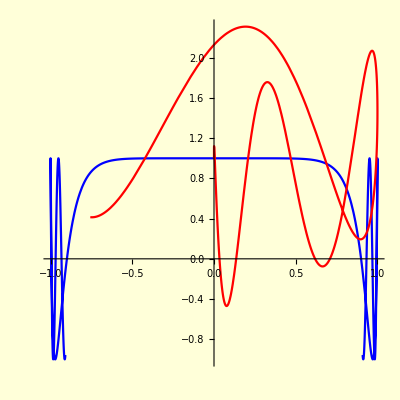

```mathematica
ParametricPlot[{p111[t],p112[t]},{t,-2,2},PlotStyle->{Blue,Red},Background->LightYellow,AspectRatio->1]
```

```mathematica
(*P10*)
G={{1,1},{1,2},{1,-1},{2,7},{3,10},{4,-9},{8,-1},{9.5,-0.8},{10,2}}
{{1,1},{1,2},{1,-1},{2,7},{3,10},{4,-9},{8,-1},{9.5,-0.8},{10,2}}
```

{{1,1},{1,2},{1,-1},{2,7},{3,10},{4,-9},{8,-1},{9.5,-0.8},{10,2}}

{{1,1},{1,2},{1,-1},{2,7},{3,10},{4,-9},{8,-1},{9.5,-0.8},{10,2}}

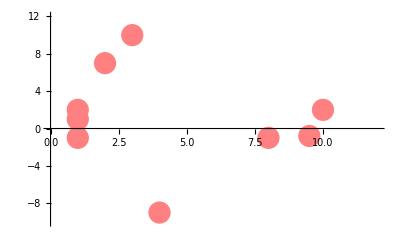

```mathematica
Plot1=ListPlot[G,PlotStyle->{PointSize[0.04],Pink},PlotRange->{{0,12},{-10,12}}]
```

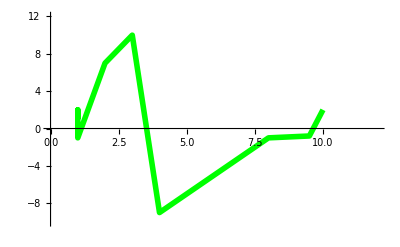

```mathematica
(*P11*)
Plot2=ListPlot[G,Joined->True,PlotStyle->{Green,Thickness[0.01]},PlotRange->{{0,12},{-10,12}}]
```

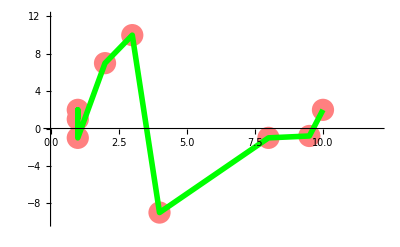

```mathematica
Show[Plot1,Plot2]
```

```mathematica
(*P12*)
f16[x_,n_]:=Cos[n*x]
```

```mathematica
Animate[Plot[f16[x,n],{x,0,2Pi}],{n,1,6,1},AnimationRunning->False]
```

```mathematica
(*P13*)
f131[x_,n_]:=Cos[n x/10]
```

```mathematica
f132[x_,n_]:=Sin[n^2 x]
```

```mathematica
Animate[Plot[{f131[x,n],f132[x,n]},{x,0,5Pi}],{n,1,10,1},AnimationRunning->False]
```

```mathematica
(*P14*)
xp[t_,n_]:=Sin[2t*n]
yp[t_,n_]:=Cos[t^2*n/10]
```

```mathematica
Animate[ParametricPlot[{xp[t,n],yp[t,n]},{t,0,5},PlotPoints->100],{n,1,10,1},AnimationRunning->False]
```

```mathematica
(*P15*)
f19[x_,y_]:=Sin[x^2-y^2]
```

```mathematica
Plot3D[f19[x,y],{x,-1,3},{y,-2,2},PlotPoints->{20,20},AxesLabel->{"Length","Width","Height"}]
```

-Graphics3D-

```mathematica
(*P16*)
f21[x_,y_,n_]:=Sin[x+y*n]
```

```mathematica
Animate[Plot3D[f21[x,y,n],{x,0,4},{y,0,2},PlotPoints->40,PlotLabel->"Animation"],{n,1,15,2},AnimationRunning->False]
```

```mathematica
Options[Plot3D];
```

```mathematica
Animate[Plot3D[f21[x,y,n],{x,0,4},{y,0,2},PlotPoints->40,PlotLabel->"Animation",ColorFunction->"BlueGreenYellow",MeshStyle->Orange],{n,1,15,2},AnimationRunning->False]
```

```mathematica
(*P18*)
```

```mathematica
x22[u_]:=Sin[u]
```

```mathematica
y22[u_]:=Cos[u]
```

```mathematica
z22[u_]:=u/10
```

```mathematica
spiral[u_]:={x22[u],y22[u],z22[u]}
```

```mathematica
ParametricPlot3D[spiral[u],{u,0,20}]
```

-Graphics3D-

```mathematica
(*P19*)
```

```mathematica
ParametricPlot3D[spiral[u],{u,0,20},ColorFunction->"Rainbow",PlotStyle->{Thick,Dashed}]
```

-Graphics3D-

```mathematica
(*P20*)
x23[u_,v_]:=u
```

```mathematica
y23[u_,v_]:=v
```

```mathematica
z23[u_,v_,n_]:=n*(u^2+v^2)/10
```

```mathematica
p23[u_,v_,n_]:={x23[u,v],y23[u,v],z23[u,v,n]}
```

```mathematica
Animate[ParametricPlot3D[p23[u,v,n],{u,-5,5},{v,-5,5},PlotRange->{{-5,5},{-5,5},{0,10}},PlotPoints->20],{n,1,3,0.5},AnimationRunning->False]
```